```mathematica
Fission Product Poisons
```

```mathematica
This notebook calculates the reactivity effects from Xe135 and Sm149 poisons.
```

## Nuclear Constants

```mathematica
v = 2.442;
σSmAbs = 4.15*^-20;
σXeAbs = 2.6*^-18;
σfuelAbs = 5.851*^-22;
λI = 2.9129*^-5;
λXe = 2.1066*^-5;
λPm = 3.63*^-6;
γI = 0.063;
γXe = 0.003;
γPm = 0.01071;
γSm = 0.01088;

ΣFuelFis = 0.1319;
ϕth[P_] = 1.9076*^7*P;
Beff = 0.0075;
$[ρ_] = ρ/Beff;

(* Six Factor Formula *)
p = 0.7;
ϵ = 1.06;
```

## Xe-135

### Concentration of Xe-135 during operation

Concentration of equilibrium Xe-135 at

5W = 3.94148×10^10 at/cc

250 kW = 1.24057×10^15 at/cc.

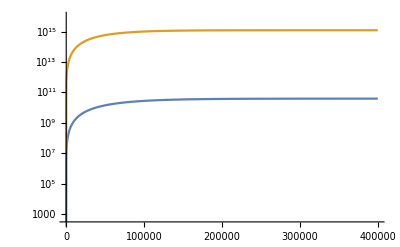

```mathematica
IEqOp[P_,t_] = (γI*ΣFuelFis*ϕth[P])/γI(1-E^(-γI*t));
a = (γXe+γI)*ΣFuelFis*ϕth[P];
b = γI*ΣFuelFis*ϕth[P];
c = λXe+σXeAbs*ϕth[P];
XeEqOp[P_,t_] = a/c-b/(c-λI)E^(-λI*t)+(c*b-a(c-λI))/(c(c-λI))Exp[-c*t];
StringForm["Concentration of equilibrium Xe-135 at"]
StringForm["5W = `` at/cc", Limit[XeEqOp[5,t],t-> Infinity]]
StringForm["250 kW = `` at/cc.", Limit[XeEqOp[250000,t],t-> Infinity]]
LogPlot[{XeEqOp[5,t],XeEqOp[250000,t]},{t,0,4*^5},PlotRange->{0,1*10^16}]
```

### Reactivity of Xe-135 during operation

```mathematica
ρXeOp[P_] = -(γI+γXe)/(v*p*ϵ)*ϕth[P]/(7.7*^12+ϕth[P]);
StringForm["Reactivity of equilibrium Xe-135 at 5W = `` %Δρ = $ ``.", ρXeOp[5], $[ρXeOp[5]]]
StringForm["Reactivity of equilibrium Xe-135 at 250 kW = `` %Δρ = $ ``.", $[ρXeOp[250000]], $[ρXeOp[250000]]]
```

Reactivity of equilibrium Xe-135 at 5W = -4.51186×10^-7 %Δρ = $ -0.0000601581.

Reactivity of equilibrium Xe-135 at 250 kW = -1.8575 %Δρ = $ -1.8575.

## Sm-149

### Concentration of Sm149

```mathematica
PmEqOp[P_] = (γPm*ΣFuelFis*ϕth[P])/λPm;
SmEqOp = (γSm*ΣFuelFis)/σSmAbs;

StringForm["Equil. concentration of Pm149 at 5W = `` at/cc.", PmEqOp[5]]
StringForm["Equil. concentration of Pm149 at 250 kW = `` at/cc.", PmEqOp[250000]]
StringForm["Equil. concentration of Sm149 at any criticality = `` at/cc.", SmEqOp]
StringForm["Equil. concentration of Sm149 after shutdown from 250 kW = `` at/cc.", PmEqOp[250000]+SmEqOp]
```

Equil. concentration of Pm149 at 5W = 3.7118×10^10 at/cc.

Equil. concentration of Pm149 at 250 kW = 1.8559×10^15 at/cc.

Equil. concentration of Sm149 at any criticality = 3.458×10^16 at/cc.

Equil. concentration of Sm149 after shutdown from 250 kW = 3.64359×10^16 at/cc.

### Reactivity of Sm149

```mathematica
ϕth[P_] = 1.9076*^7*P;
ρSmOp = -γSm/(v*p*ϵ);
$SmOp = $[ρSmOp];
ρSmSd[P_] = -γPm/(v*p*ϵ)(1+(σSmAbs*ϕth[P])/λPm)
ρSmSd[5]
$[ρSmSd[5]]
ρSmSd[250000]
$[ρSmSd[250000]]
```

-0.00591071 (1+2.18087×10^-7 P)

-0.00591072

-0.788096

-0.00623298

-0.831063